# Notebook to generate Flash Cards using the Unit Step function

## Set Parameters

This notebook is used to develop plots of the a) the unit step function and b) a core function times the unit step function.

Each final plot is a compilation of 3 plot : 1) core * unit step function (plotStyle1), 2) unfiltered core function (plotStyle2), and 3) unit step function (plotStyle3).

Set the current directory as working directory to export files.

```mathematica
SetDirectory[NotebookDirectory[]];
```

Choose the export format for plots.

```mathematica
outExt = {".pdf",".png"}
opt = 1
```

{.pdf,.png}

1

Parameters: 3 different plot styles and 1 label style

```mathematica
(* core * unit step *)
plotStyle1=Directive[Bold,Black,Thickness[0.005]];
(* full unfiltered core *)
plotStyle2=Directive[Dashed,Thickness[0.002]];
(* unit step *)
plotStyle3=Directive[Dashing[0.05],Red,Thickness[0.02]];
(* style of plot labels *)
labelStyle = {FontSize->14,FontFamily->"Courier New",Bold};
```

#### Font Families

Note, there are MANY font families. See the list using $FontFamilies. Here is the list shown in their font.

```mathematica
Style[#,FontFamily->#]&/@$FontFamilies
```

{Al Bayan,Alegreya SC,Al Nile,Al Tarikh,American Typewriter,Andale Mono,Apple Braille,Apple Chancery,Apple Color Emoji,AppleGothic,AppleMyungjo,Apple SD Gothic Neo,Apple Symbols,Arial,Arial Black,Arial Hebrew,Arial Hebrew Scholar,Arial Narrow,Arial Rounded MT Bold,Arial Unicode MS,Athelas,Avenir,Avenir Next,Avenir Next Condensed,Ayuthaya,Baghdad,Bangla MN,Bangla Sangam MN,Baskerville,Beirut,Big Caslon,Bitstream Vera Sans Mono,Bodoni 72,Bodoni 72 Oldstyle,Bodoni 72 Smallcaps,Bodoni Ornaments,Bradley Hand,Brush Script MT,Chalkboard,Chalkboard SE,Chalkduster,Charter,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Cochin,Comic Sans MS,Copperplate,Corsiva Hebrew,Courier,Courier New,Cousine,Damascus,DecoType Naskh,Devanagari MT,Devanagari Sangam MN,Didot,DIN Alternate,DIN Condensed,Diwan Kufi,Diwan Thuluth,Droid Serif,EB Garamond,EB Garamond 12 All SC,EB Garamond SC,Economica,Euphemia UCAS,Farah,Farisi,Felipa,Futura,GB18030 Bitmap,Geeza Pro,Geneva,Gentium Basic,Georgia,Gill Sans,Gujarati MT,Gujarati Sangam MN,Gurmukhi MN,Gurmukhi MT,Gurmukhi Sangam MN,Heiti SC,Heiti TC,Helvetica,Helvetica Neue,Herculanum,Hiragino Kaku Gothic Pro,Hiragino Kaku Gothic ProN,Hiragino Kaku Gothic Std,Hiragino Kaku Gothic StdN,Hiragino Maru Gothic Pro,Hiragino Maru Gothic ProN,Hiragino Mincho Pro,Hiragino Mincho ProN,Hiragino Sans,Hiragino Sans GB,Hoefler Text,Impact,InaiMathi,Inconsolata,Iowan Old Style,ITF Devanagari,ITF Devanagari Marathi,Kailasa,Kaiti SC,Kaiti TC,Kalam,Kannada MN,Kannada Sangam MN,Kefa,Khmer MN,Khmer Sangam MN,Kohinoor Bangla,Kohinoor Devanagari,Kohinoor Telugu,Kokonor,Krungthep,KufiStandardGK,Lao MN,Lao Sangam MN,Lato,League Gothic,Lucida Grande,Luminari,Malayalam MN,Malayalam Sangam MN,Marion,Marker Felt,Menlo,Microsoft Sans Serif,Mishafi,Mishafi Gold,Monaco,Mshtakan,Muna,Myanmar MN,Myanmar Sangam MN,Nadeem,New Peninim MT,Noteworthy,Noto Nastaliq Urdu,Optima,Oriya MN,Oriya Sangam MN,Osaka,Oswald,Palatino,Papyrus,Phosphate,PingFang HK,PingFang SC,PingFang TC,Plantagenet Cherokee,Playfair Display,PT Mono,PT Sans,PT Sans Caption,PT Sans Narrow,PT Serif,PT Serif Caption,Raanana,Roboto,Roboto Condensed,Roboto Slab,Rockwell,Sana,Sathu,Savoye LET,Seravek,Shadows Into Light Two,Shree Devanagari 714,SignPainter,Silom,Sinhala MN,Sinhala Sangam MN,Skia,Snell Roundhand,Songti SC,Songti TC,Source Code Pro,Source Sans Pro,Source Serif Pro,STFangsong,STHeiti,STIXGeneral,STIXIntegralsD,STIXIntegralsSm,STIXIntegralsUp,STIXIntegralsUpD,STIXIntegralsUpSm,STIXNonUnicode,STIXSizeFiveSym,STIXSizeFourSym,STIXSizeOneSym,STIXSizeThreeSym,STIXSizeTwoSym,STIXVariants,STKaiti,STSong,Sukhumvit Set,Superclarendon,Symbol,Tahoma,Tamil MN,Tamil Sangam MN,Telugu MN,Telugu Sangam MN,Thonburi,Times,Times New Roman,Titillium Web,Trattatello,Trebuchet MS,Verdana,Waseem,Webdings,Wingdings,Wingdings 2,Wingdings 3,Yanone Kaffeesatz,Zapf Dingbats,Zapfino}

## Auxiliary functions

Function to export plots to files

```mathematica
fileExport[name_String]:=Module[{},
(* Export unit step plot *)
Export[name<>"unitstep" <> outExt[[opt]],p3];
(* Export combined plot *)
Export[name<>outExt[[opt]],plot];
]
```

```mathematica
equationExport[name_String] := Export[name<>".txt","y(t) =" <> StringReplace[ToString[TeXForm[unitStep]],"\\theta"->"\\mathscr{U}"]]
```

```mathematica
plot1 := Plot[core*ReleaseHold[unitStep],domain,GridLines->Automatic,Filling->None,PlotStyle->plotStyle1,PlotRange->range, LabelStyle->labelStyle]
plot2 := Plot[core,domain,PlotStyle->plotStyle2,LabelStyle->labelStyle]
plot3 := Plot[ReleaseHold[unitStep],domain,GridLines->Automatic,PlotStyle->plotStyle3,Filling->Axis, PlotRange->1.05*range, AxesLabel -> {t, y},LabelStyle->labelStyle]
```

## Example 1

Set file names

```mathematica
name = "example1";
```

Core & unit step

```mathematica
core = 1/20t^2;
unitStep = HoldForm[UnitStep[t-1.5]];
```

Set plot domain and range

```mathematica
domain = {t,0,6};
range={0,2.05};
```

Plot 1: core * unit step

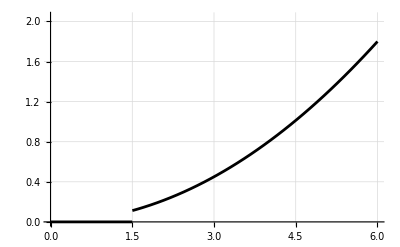

```mathematica
p1=plot1
```

plot 2: core without unit step

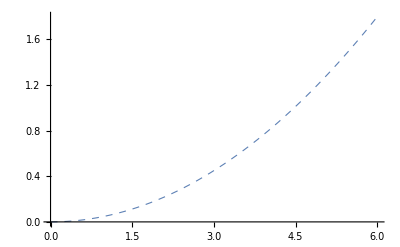

```mathematica
p2=plot2
```

Plot 3 : unit step

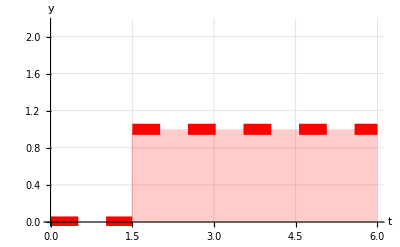

```mathematica
p3=plot3
```

Combine plots

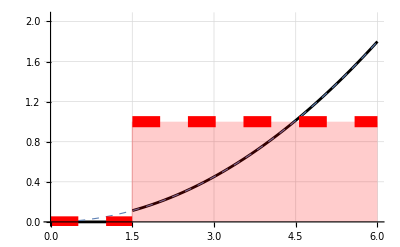

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example1.txt

## Example 2

Set file names

```mathematica
name = "example2";
```

Core & unit step

```mathematica
core = 1/4t^2;
unitStep = HoldForm[(UnitStep[t-0.5]-UnitStep[t-2.5])];
```

Set plot domain and range

```mathematica
domain = {t,0,4};
range={0,1.05};
```

Plot 1: core * unit step

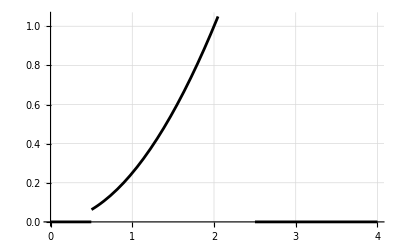

```mathematica
p1=plot1
```

plot 2: core without unit step

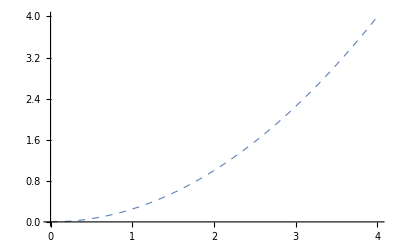

```mathematica
p2=plot2
```

Plot 3 : unit step

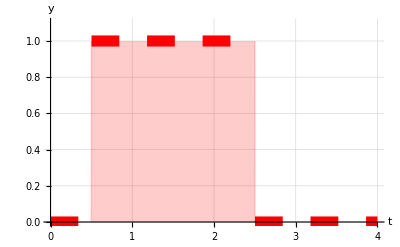

```mathematica
p3=plot3
```

Combine plots

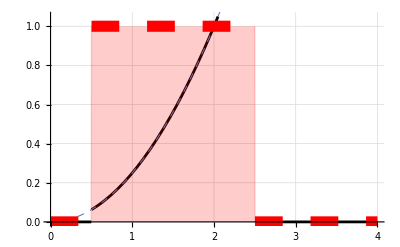

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example2.txt

## Example 3

Set file names

```mathematica
name = "example3";
```

Core & unit step

```mathematica
core = 1/25t^2;
unitStep = HoldForm[(UnitStep[t-1]+UnitStep[t-2]+UnitStep[t-3])];
```

```mathematica
unitStep
```

UnitStep[t-1]+UnitStep[t-2]+UnitStep[t-3]

Set plot domain and range

```mathematica
domain = {t,0,4};
range={0,4.05};
```

Plot 1: core * unit step

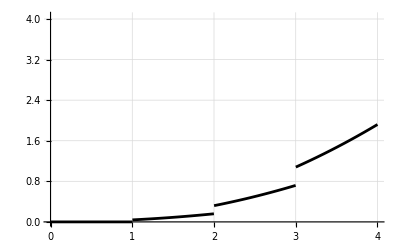

```mathematica
p1=plot1
```

plot 2: core without unit step

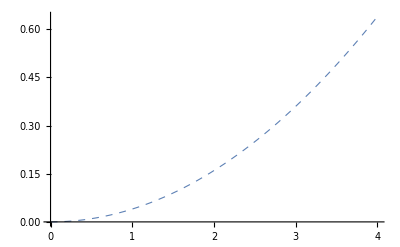

```mathematica
p2=plot2
```

Plot 3 : unit step

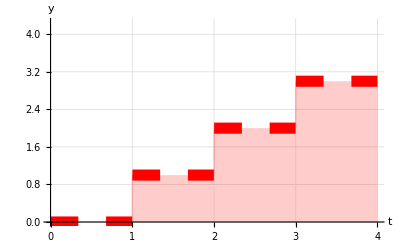

```mathematica
p3=plot3
```

Combine plots

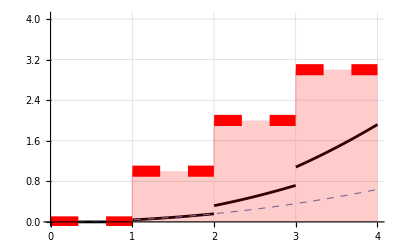

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example3.txt

## Example 4

Set file names

```mathematica
name = "example4";
```

Core & unit step

```mathematica
core = Sin[π t];
unitStep = HoldForm[(UnitStep[t-2]-UnitStep[t-4])];
```

Set plot domain and range

```mathematica
domain = {t,0,6};
range={-1.05,1.05};
```

Plot 1: core * unit step

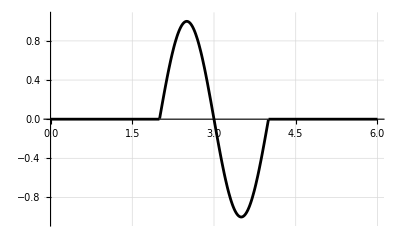

```mathematica
p1=plot1
```

plot 2: core without unit step

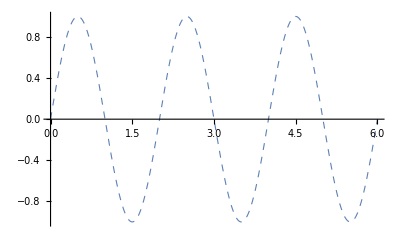

```mathematica
p2=plot2
```

Plot 3 : unit step

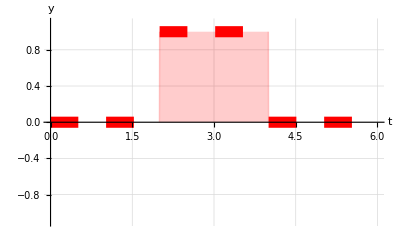

```mathematica
p3=plot3
```

Combine plots

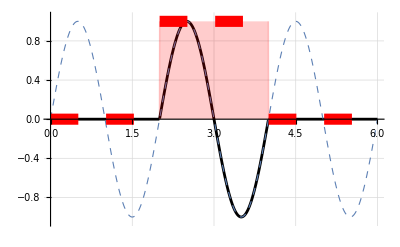

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example4.txt

## Example 5

Set file names

```mathematica
name = "example5";
```

Core & unit step

```mathematica
core = Sin[π t];
unitStep = HoldForm[(1-UnitStep[t-1]+UnitStep[t-2])];
```

Set plot domain and range

```mathematica
domain = {t,0,4};
range={-1.05,1.05};
```

Plot 1: core * unit step

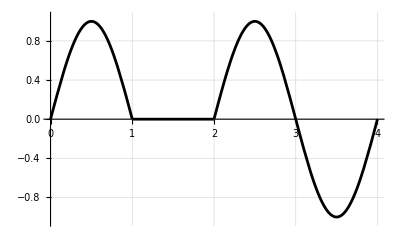

```mathematica
p1=plot1
```

plot 2: core without unit step

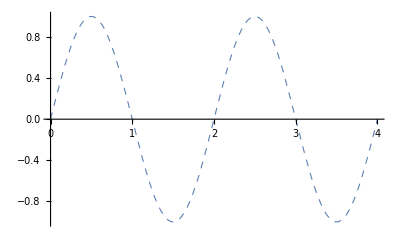

```mathematica
p2=plot2
```

Plot 3 : unit step

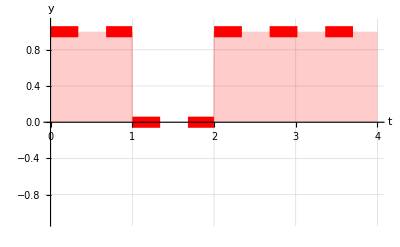

```mathematica
p3=plot3
```

Combine plots

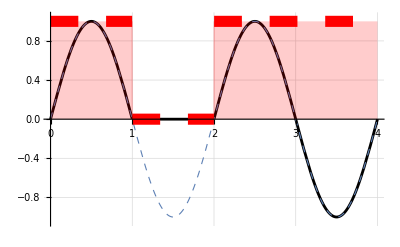

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example5.txt

## Example 6

Set file names

```mathematica
name = "example6";
```

Core & unit step

```mathematica
core = Sin[π t];
unitStep = HoldForm[(1-UnitStep[t-1])];
```

Set plot domain and range

```mathematica
domain = {t,0,4};
range={-1.05,1.05};
```

Plot 1: core * unit step

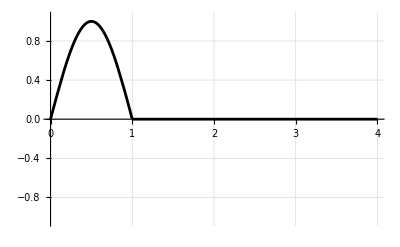

```mathematica
p1=plot1
```

plot 2: core without unit step

```mathematica
p2=plot2
```

-Graphics-

Plot 3 : unit step

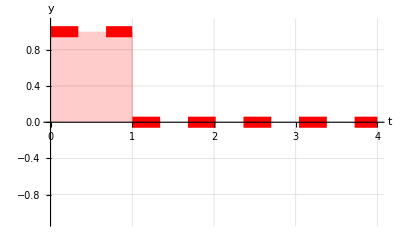

```mathematica
p3=plot3
```

Combine plots

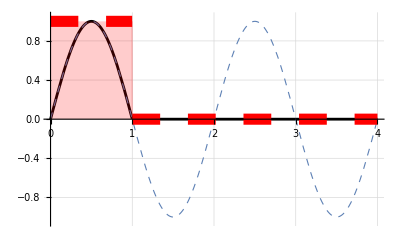

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example6.txt

## Example 7

Set file names

```mathematica
name = "example7";
```

Core & unit step

```mathematica
core = Sin[π t];
unitStep = HoldForm[(-UnitStep[t-2]+UnitStep[t-4])];
```

Set plot domain and range

```mathematica
domain = {t,0,6};
range={-1.05,1.05};
```

Plot 1: core * unit step

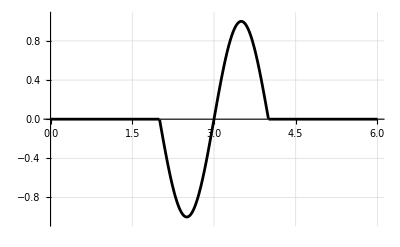

```mathematica
p1=plot1
```

plot 2: core without unit step

```mathematica
p2=plot2
```

-Graphics-

Plot 3 : unit step

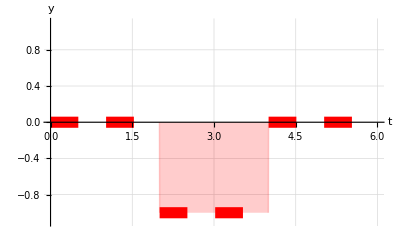

```mathematica
p3=plot3
```

Combine plots

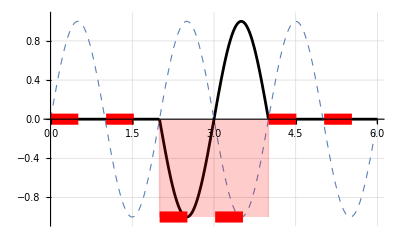

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example7.txt

## Example 8

Set file names

```mathematica
name = "example8";
```

Core & unit step

```mathematica
core = Sin[π t];
unitStep = HoldForm[(1-2UnitStep[t-2])];
```

Set plot domain and range

```mathematica
domain = {t,0,6};
range={-1.05,1.05};
```

Plot 1: core * unit step

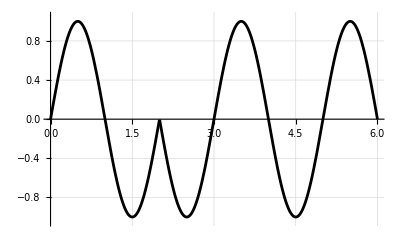

```mathematica
p1=plot1
```

plot 2: core without unit step

```mathematica
p2=plot2
```

-Graphics-

Plot 3 : unit step

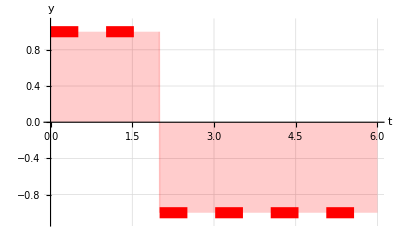

```mathematica
p3=plot3
```

Combine plots

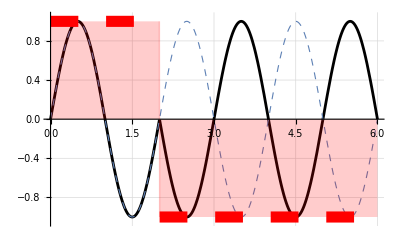

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example8.txt

## Example 9

Set file names

```mathematica
name = "example9";
```

Core & unit step

```mathematica
core = Sin[π t];
unitStep = HoldForm[(2-UnitStep[t-1]-UnitStep[t-2])];
```

Set plot domain and range

```mathematica
domain = {t,0,6};
range={-1.05,2.05};
```

Plot 1: core * unit step

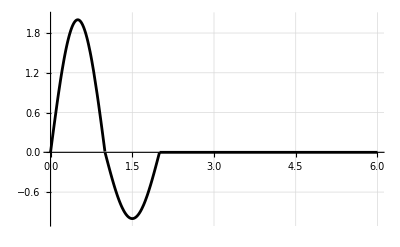

```mathematica
p1=plot1
```

plot 2: core without unit step

```mathematica
p2=plot2
```

-Graphics-

Plot 3 : unit step

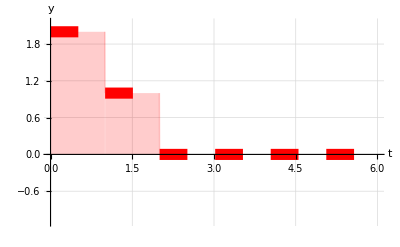

```mathematica
p3=plot3
```

Combine plots

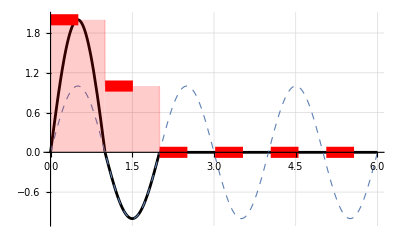

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example9.txt

## Example 10

Set file names

```mathematica
name = "example10";
```

Core & unit step

```mathematica
core = t;
unitStep = HoldForm[(-1+2UnitStep[t-2])];
```

Set plot domain and range

```mathematica
domain = {t,0,4};
range={-2.05,4.05};
```

Plot 1: core * unit step

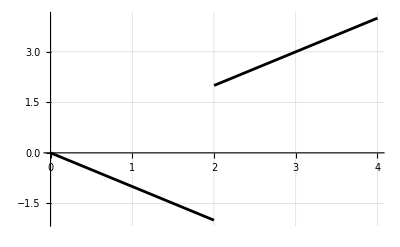

```mathematica
p1=plot1
```

plot 2: core without unit step

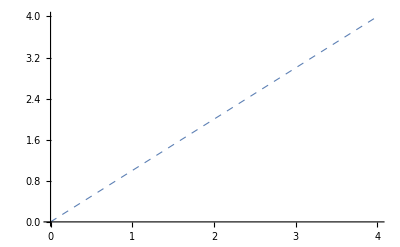

```mathematica
p2=plot2
```

Plot 3 : unit step

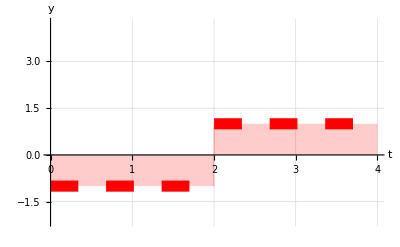

```mathematica
p3=plot3
```

Combine plots

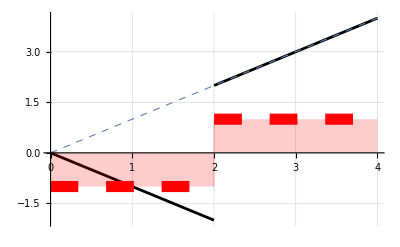

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example10.txt

## Example 11

Set file names

```mathematica
name = "example11";
```

Core & unit step

```mathematica
core = t;
unitStep = HoldForm[(-1+UnitStep[t-1.25]+UnitStep[t-2.25])];
```

Set plot domain and range

```mathematica
domain = {t,0,4};
range={-2.05,4.05};
```

Plot 1: core * unit step

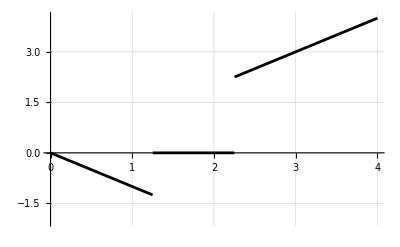

```mathematica
p1=plot1
```

plot 2: core without unit step

```mathematica
p2=plot2
```

-Graphics-

Plot 3 : unit step

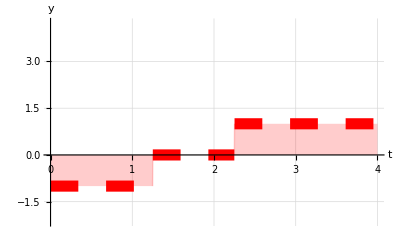

```mathematica
p3=plot3
```

Combine plots

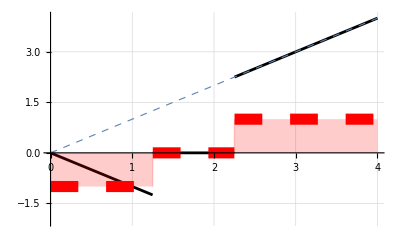

```mathematica
plot=Show[p1,p2,p3]
```

#### Export files

```mathematica
fileExport[name]
equationExport[name]
```

example11.txt